```mathematica
(*
I made this program when I conducted Compton Scattering lab.
This program imports two.spe files(Background and Actual trial) from the current directory, and it performs background subtraction to remove noise. Then, it performs gaussian fitting to extract fitting parameter. Also, callibration factor was extracted using the same method.*)
```

#### Import and format data

```mathematica
(*Get the filepath of current working directory*)
ClearAll["Global`*"]
notepath=NotebookDirectory[];
```

```mathematica
(*Import background data (dataBG) and actual data (dataACT)*)
SetDirectory[notepath];
dataBG =Import[#,"List"]&/@FileNames["*_bg.spe"]//Flatten;(*search file that contains "_bg.spe"*)

dataACT=Import[#,"List"]&/@FileNames["*_act.spe"]//Flatten;
```

```mathematica
(*Extaract file base name*)SetDirectory[notepath];
base = FileBaseName[FileNames["*_act.spe"]⟦1⟧];
```

```mathematica
(*Format data (Orginal data contains letters, so it gets rid of them.)*)
dataBG=dataBG⟦13;;Length[dataBG]-19⟧;
dataACT=dataACT⟦13;;Length[dataACT]-19⟧;
```

```mathematica
(*Perform background subtraction*)
dataSubtracted=dataACT-dataBG;
```

```mathematica
(*Create a directory to export csv files later.*)
SetDirectory[notepath];DeleteDirectory["bg_Subtracted",DeleteContents->True]
newdirectory = CreateDirectory[File["bg_Subtracted"]];
```

```mathematica
(*Export the resulted data as csv*)
SetDirectory[newdirectory];
Export[ToString[base]<>".csv",dataSubtracted,"CSV"];
```

#### Perform Gaussian Fit

```mathematica
min=1;
max=4093;
guessCenter=2250;
```

```mathematica
(* g1 is the list plot of background subtracted data*)
g1=ListPlot[dataSubtracted⟦min;;max⟧,PlotRange->{0,100},ImageSize->Large];
```

Fit with Gaussian

```mathematica
(*Fitting Parameter:
A1:Height of the peak,
  A2:Centroid of the peak,
  A3:Peak area
 *)
nlm=NonlinearModelFit[dataSubtracted,A1 Exp[-(x-A2)^2/(2 A3^2)],{{A1},{A2,guessCenter},{A3}},x];
```

```mathematica
(*g2 is the fitting curve*)
```

```mathematica
g2  = Plot[nlm[t],{t,0,max-min},PlotStyle->Red,PlotRange->All];
```

{A1→30.1197,A2→2229.27,A3→182.802}

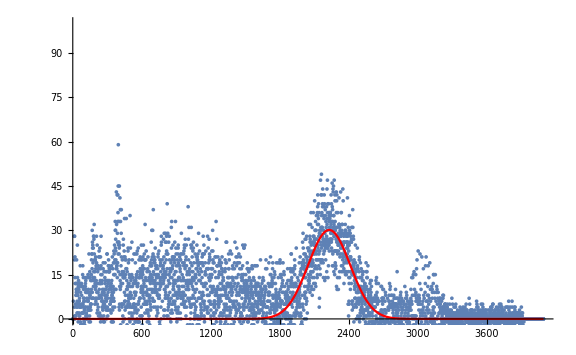

```mathematica
(*Show the fitting parameter and resulted graph*)
Print[nlm["BestFitParameters"]]
Show[g1,g2]
```